Результаты по методу Эйлера

|   x |   y
 |  0.78540 |  0.50000
 |  0.83540 |  0.50000
 |  0.88540 |  0.49487
 |  0.93540 |  0.48464
 |  0.98540 |  0.46939
 |  1.03540 |  0.44925
 |  1.08540 |  0.42440
 |  1.13540 |  0.39506
 |  1.18540 |  0.36149
 |  1.23540 |  0.32400

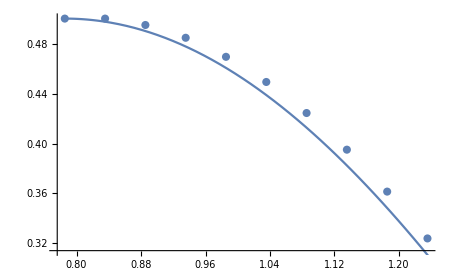

```mathematica
(*Вариант 4*)
f[x_,y_]:=(Cos[x])^2-y*Tan[x];
h=0.05;
a=0.25*π;b=0.4*π;
(*Решение методом Эйлера*)
y0=0.5;
x0=a;
m=Floor[(b-a)/h]+1;
x=x0;y=y0;
eu1=Table[{x,y}={x+h,y+h*f[x,y]},{i,m-1}];
eu1=Prepend[eu1,{x0,y0}];
Print["Результаты по методу Эйлера"];
gr1:=ListPlot[eu1];
lst={{},{"  x","  y"}};
PaddedForm[TableForm[eu1, TableHeadings->lst],{5,5}]
(*для контроля сравним полученный результат с точным решением ДУ*)
g[x_]:=0.5*Sin[2*x]
gr2:=Plot[g[x],{x,a,b}]
Show[{gr1,gr2}]
```

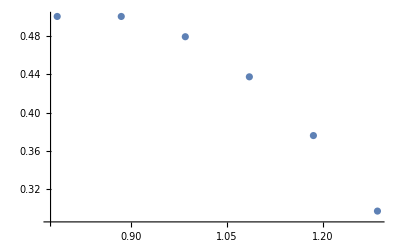

-Graphics-